```mathematica
possibleMasses=Table[If[Length[NSolve[specificDrag==2dragCoefficient airDensity dragArea (payloadMass+dragArea dragMassPerArea+.5(springMass+hingeMass))totalEnergy/((payloadMass+dragArea dragMassPerArea+springMass+hingeMass)^3 gravity)&&dragArea>0,dragArea]]>0,True,False],{payloadMass,0,5,.01},{dragMassPerArea,0,1,.01}];
```

```mathematica
Show[ArrayPlot[possibleMasses/.{True->1,False->0}],Graphics[{Red,Line[{{48,0},{48,500}}],Blue,Line[{{0,400},{100,400}}]}]]
```

-Graphics-

```mathematica
(Total[possibleMasses⟦All,49⟧/.{True->1,False->0}]-2)/100.
```

0.08

```mathematica
ClearAll[specificDrag]
specificDrag[dragArea_,payloadMass_,length_]:=2dragCoefficient airDensity dragArea (payloadMass+dragArea dragMassPerArea+.5(density numberOfSprings width thickness length+hingeMass))totalEnergy/((payloadMass+dragArea dragMassPerArea+density numberOfSprings width thickness length+hingeMass)^3 gravity)
```

```mathematica
ClearAll[efficiency]
efficiency[dragArea_,payloadMass_,length_]:=(payloadMass+.5(density numberOfSprings width thickness length+hingeMass))/(payloadMass+dragArea dragMassPerArea+density numberOfSprings width thickness length+hingeMass)
```

```mathematica
ClearAll[velocity]
velocity[dragArea_,payloadMass_,length_]:=√((2efficiency[dragArea,payloadMass]springEnergy[length,10])/(payloadMass+dragArea dragMassPerArea+density numberOfSprings width thickness length+hingeMass))
```

```mathematica
ClearAll[springEnergy]
springEnergy[length_,numberOfElements_]:=With[{compressedLength=.23length,dLength=uncompressedLength/numberOfElements,secondMomentOfArea=width thickness^3/12,energy=Function[{deflection},Total[numberOfElements elasticModulus width thickness^3 deflection^2/(24uncompressedLength) ]],deflection=Array[d,numberOfElements]},Minimize[{energy[deflection],Total[dLength Cos[Accumulate[deflection]]]==0,Total[dLength Sin[Accumulate[deflection]]]==0},deflection]]
```

```mathematica
springEnergy[uncompressedLength,numberOfElements]
```

{0.326382,{d[1]→-1.08136×10^-8,d[2]→0.165138,d[3]→0.350124,d[4]→0.560063,d[5]→0.756854,d[6]→0.844074,d[7]→0.756854,d[8]→0.560063,d[9]→0.350124,d[10]→0.165138}}

```mathematica
uncompressedLength=.25;
compressedLength=.23uncompressedLength;
width=.0047752;
thickness=.0004826;
numberOfSprings=4;
elasticModulus=131 10^9;
density=1500;
numberOfElements=10;
dragCoefficient=1.4;
airDensity=1.225;
gravity=9.81;
hingeMass=0.02;
```

```mathematica
desiredVelocity=10;
desiredVelocityMargin=10;
NSolve[{specificDrag[dragArea,payloadMass]==10,Abs[velocity[dragArea,payloadMass]-desiredVelocity]<desiredVelocityMargin},{dragArea,payloadMass}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(121001 dragArea)/175984-(92291 payloadMass)/87992 == 1.

{}

```mathematica
dataRange={{0.0,0.3},{0.1,1}};
{specificDrags,velocities}=Table[#[π dragRadius^2,0,springLength],{dragRadius,dataRange⟦1,1⟧,dataRange⟦1,2⟧,0.001},{springLength,dataRange⟦2,1⟧,dataRange⟦2,2⟧,0.01}]&/@{specificDrag,velocity};
```

$Aborted

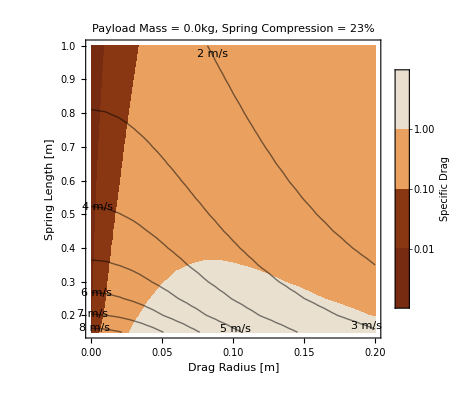

```mathematica
Show[ListContourPlot[specificDrags,PlotRange->All,Contours->{0.01,0.1,1,10,100},ContourStyle->None,ColorFunctionScaling->False,DataRange->dataRange,ColorFunction->ColorData["SiennaTones"],PlotLegends->BarLegend[Automatic,LegendLabel->"Specific Drag"],FrameLabel->{"Drag Radius [m]","Spring Length [m]"},PlotLabel->"Payload Mass = 0.0kg, Spring Compression = 23%"],ListContourPlot[velocities,ContourShading->None,ContourStyle->Thick,ContourLabels->Function[{x,y,z},Text[Quantity[z,"meters per second"],{x,y},Background->White]],DataRange->dataRange],ImageSize->Full]
```

```mathematica
Export[NotebookDirectory[]<>StringRiffle[DateList[]⟦1;;-2⟧,"."]<>"_JumperConfigurationSpace.png",%]
```

/Users/fp/projects/Jumping Robots/2019.7.25.17.29_JumperConfigurationSpace.png

```mathematica
StringRiffle[DateList[]⟦1;;-2⟧,"."]//FullForm
```

"2019.7.25.17.24"

```mathematica
velocities=Import[NotebookDirectory[]<>"velocity.csv", "CSV"];
specificDrags=Import[NotebookDirectory[]<>"specificDrag.csv", "CSV"];
dataRange={{0,.2},{.15,1}};
```

```mathematica
ToString[3]
```

3